```mathematica
3(2k+1)+1
```

1+3 (1+2 k)

```mathematica
Simplify[1+3 (1+2 k)]
```

4+6 k

```mathematica
4+2(3k)
```

4+6 k

```mathematica
EvenQ[2k]
```

False

```mathematica
f[x_]:=(1+Cos[π x])/2
```

```mathematica
(1-f[x])(3x+1)+f[x](x/2)
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

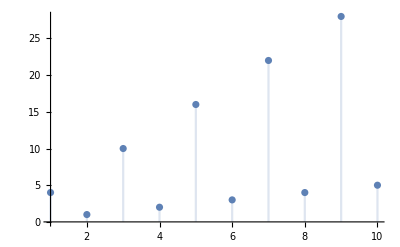

```mathematica
DiscretePlot[(1-f[x])(3x+1)+f[x](x/2),{x,1,10}]
```

```mathematica
Nest[f,x,2]
```

1/2 (1+Cos[1/2 π (1+Cos[π x])])

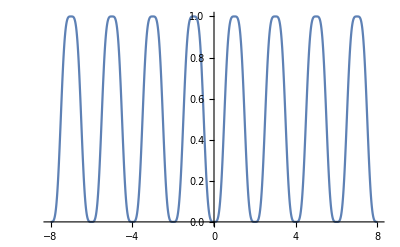

```mathematica
Plot[1/2 (1+Cos[1/2 π (1+Cos[π x])]),{x,-8,8}]
```

```mathematica
f[x_]:=(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])
```

```mathematica
Nest[f,x,2]
```

(1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))])

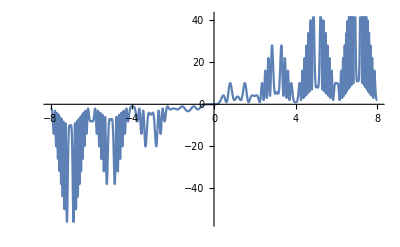

```mathematica
Plot[%12,{x,-8,8}]
```

```mathematica
f[x]
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

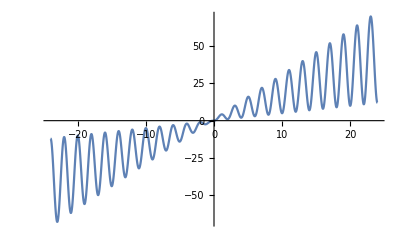

```mathematica
Plot[(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
f[x]
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

```mathematica
f[2]
```

1

```mathematica
f[3]
```

10

```mathematica
f[f]
```

(1+3 f) (1+1/2 (-1-Cos[f π]))+1/4 f (1+Cos[f π])

```mathematica
f[f[x]]
```

(1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))])

```mathematica
f[f[f[x]]]
```

(1+3 ((1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))]))+1/4 ((1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))])) (1+Cos[π ((1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))])

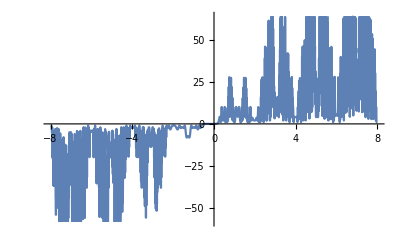

```mathematica
Plot[%21,{x,-8,8}]
```

```mathematica
Manipulate[
Plot[Nest[f,x,i],{x,1,10}]
,{i,1,10,1}]
```

```mathematica
Manipulate[
DiscretePlot[Nest[f,x,i],{x,1,20}]
,{i,1,10,1}]
```

```mathematica
Table[Nest[f,x,i],{i,1,5}]
```

{(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),3,(1+3 ((1) (1)+1)) (1+1)+1}
 |  |  |  |

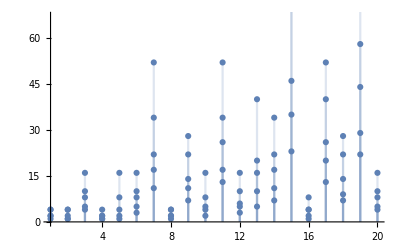

```mathematica
DiscretePlot[Out[27],{x,1,20}]
```

```mathematica
Manipulate[
DiscretePlot[Nest[f,x,i],{x,1,20},PlotRange->{1,50}]
,{i,1,10,1}]
```

```mathematica
f[f[x]]
```

(1+3 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))) (1+1/2 (-1-Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))]))+1/4 ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])) (1+Cos[π ((1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]))])

```mathematica
FullSimplify[f[f[x]],x∈Reals]
```

1/16 (22+49 x-14 Cos[π x]-35 x Cos[π x]+(-18-35 x+5 (2+5 x) Cos[π x]) Sin[1/4 π (-7 x+(2+5 x) Cos[π x])])

```mathematica
TrigReduce[1/16 (22+49 x-14 Cos[π x]-35 x Cos[π x]+(-18-35 x+5 (2+5 x) Cos[π x]) Sin[1/4 π (-7 x+(2+5 x) Cos[π x])])]
```

1/32 (44+98 x-28 Cos[π x]-70 x Cos[π x]-36 Sin[1/4 π (-7 x+(2+5 x) Cos[π x])]-70 x Sin[1/4 π (-7 x+(2+5 x) Cos[π x])]-10 Sin[π x-1/4 π (-7 x+(2+5 x) Cos[π x])]-25 x Sin[π x-1/4 π (-7 x+(2+5 x) Cos[π x])]+10 Sin[π x+1/4 π (-7 x+(2+5 x) Cos[π x])]+25 x Sin[π x+1/4 π (-7 x+(2+5 x) Cos[π x])])

```mathematica
Plot[1/16 (22+49 x-14 Cos[π x]-35 x Cos[π x]+(-18-35 x+5 (2+5 x) Cos[π x]) Sin[1/4 π (-7 x+(2+5 x) Cos[π x])]),{x,-8,8}]
```

-Graphics-

```mathematica
Quantity[295,"Kilobits"]/Quantity[1,"Seconds"]
```

295 kb/s

```mathematica
2.5 Quantity[295,"Kilobits"]/Quantity[1,"Seconds"]
```

737.5 kb/s

```mathematica
3 Quantity[295,"Kilobits"]/Quantity[1,"Seconds"]
```

885 kb/s

```mathematica
EntityClassList["Financial"]
```

{Advertising Agencies,Agricultural Inputs,Airlines,Airports And Air Services,Aluminum,Apparel Manufacturing,Apparel Stores,Asset Management,Auto And Truck Dealerships,Auto Manufacturers,Auto Parts,Banks Global,Banks Regional US,Beverages Brewers,Beverages Soft Drinks,Beverages Wineries And Distilleries,Biotechnology,Broadcasting Radio,Broadcasting TV,Building Materials,Business Equipment,Business Services,Capital Markets,Chemicals,Coal,Communication Equipment,Computer Distribution,Computer Systems,Confectioners,Conglomerates,Consumer Electronics,Contract Manufacturers,Copper,Credit Services,Data Storage,Department Stores,Diagnostics And Research,Discount Stores,Diversified Industrials,Drug Manufacturers Major,Drug Manufacturers Specialty And Generic,Education And Training Services,Electronic Components,Electronic Gaming And Multimedia,Electronics Distribution,Engineering And Construction,Farm And Construction Equipment,Farm Products,Food Distribution,Footwear And Accessories,Gambling,Gold,Grocery Stores,Health Care Plans,Health Information Services,Home Furnishings And Fixtures,Home Improvement Stores,Household And Personal Products,Industrial Distribution,Industrial Metals And Minerals,Information Technology Services,Infrastructure Operations,Insurance Brokers,Insurance Life,Insurance Property And Casualty,Insurance Reinsurance,Insurance Specialty,Integrated Shipping And Logistics,Internet Content And Information,Leisure,Lodging,Long Term Care Facilities,Lumber And Wood Production,Luxury Goods,Marketing Services,Media Diversified,Medical Care,Medical Devices,Medical Instruments And Supplies,Metal Fabrication,Oil And Gas Drilling,Oil And Gas E And P,Oil And Gas Equipment And Services,Oil And Gas Integrated,Oil And Gas Midstream,Oil And Gas Refining And Marketing,Packaged Foods,Packaging And Containers,Paper And Paper Products,Pay TV,Personal Services,Pharmaceutical Retailers,Pollution And Treatment Controls,Publishing,Railroads,Real Estate General,Real Estate Services,Recreational Vehicles,REIT Diversified,REIT Healthcare Facilities,REIT Hotel And Motel,REIT Industrial,REIT Office,REIT Residential,REIT Retail,Rental And Leasing Services,Residential Construction,Resorts And Casinos,Restaurants,Rubber And Plastics,Savings And Cooperative Banks,Scientific And Technical Instruments,Security And Protection Services,Semiconductor Equipment And Materials,Semiconductor Memory,Semiconductors,Shipping And Ports,Silver,Software Application,Software Infrastructure,Specialized Health Services,Specialty Chemicals,Specialty Finance,Specialty Retail,Staffing And Outsourcing Services,Steel,Telecom Services,Textile Manufacturing,Tobacco,Tools And Accessories,Trucking,Truck Manufacturing,Utilities Diversified,Utilities Regulated Electric,Utilities Regulated Gas,Utilities Regulated Water,Waste Management,Advertising And Marketing Services,Aerospace And Defense,Application Software,Autos,Banks,Beverages Alcoholic,Brokers And Exchanges,Communication Services,Computer Hardware,Consulting And Outsourcing,Consumer Packaged Goods,Drug Manufacturers,Entertainment,Health Care Providers,Homebuilding And Construction,Industrial Products,Insurance,Manufacturing Apparel And Furniture,Medical Diagnostics And Research,Medical Distribution,Metals And Mining,REI Ts,Retail Apparel And Specialty,Retail Defensive,Tobacco Products,Transportation And Logistics,Travel And Leisure,Utilities Regulated,indices,bank loan funds,bear market funds,commodities broad basket funds,communications funds,conservative allocation funds,consumer discretionary funds,consumer staples funds,convertibles funds,currency funds,diversified emerging markets funds,diversified Pacific/Asia funds,emerging markets bond funds,equity energy funds,equity precious metals funds,Europe stock funds,financial funds,foreign large cap blend funds,foreign large cap growth funds,foreign large cap value funds,foreign small/mid cap growth funds,foreign small/mid cap value funds,global real estate funds,health funds,high yield bond funds,high yield municipal funds,industrials funds,inflation-protected bond funds,intermediate government funds,intermediate-term bond funds,Japan stock funds,large cap blend funds,large cap growth funds,large cap value funds,Latin America stock funds,long government funds,long-short funds,long-term bond funds,mid-cap blend funds,mid-cap growth funds,mid-cap value funds,miscellaneous sector funds,moderate allocation funds,money market - taxable funds,money market - tax-free funds,multisector bond funds,municipal California intermediate/short funds,municipal California long funds,municipal Massachusetts funds,municipal Minnesota funds,municipal national intermediate funds,municipal national long funds,municipal national short funds,municipal New Jersey funds,municipal New York intermediate/short funds,municipal New York long funds,municipal ohio funds,municipal pennsylvania funds,municipal single state intermediate funds,municipal single state long funds,municipal single state short funds,natural resources funds,Pacific/Asia excluding Japan funds,real estate funds,retirement income funds,short government funds,short-term bond funds,small cap blend funds,small cap growth funds,small cap value funds,specialty-financial funds,specialty-natural resources funds,target date 2000-2010 funds,target date 2011-2015 funds,target date 2016-2020 funds,target date 2021-2025 funds,target date 2026-2030 funds,target-date 2030+ funds,target date 2031-2035 funds,target date 2036-2040 funds,target date 2041-2045 funds,target date 2050+ funds,technology funds,ultrashort bond funds,utilities funds,world allocation funds,world bond funds,world stock funds,AB Funds Trust,ABN AMRO Mutual Funds,Absolute Investment Advisors Mutual Funds,Absolute Strategies Mutual Funds,Acadian Mutual Funds,Accessor Mutual Funds,Activa Mutual Funds,Adams Harkness Mutual Funds,Advance Capital I Mutual Funds,AdvisorOne Mutual Funds,Advisor Series Trust Mutual Funds,Advisors Inner Circle Fund,Advisors Inner Circle II Mutual Funds,Aegis Value Mutual Funds,AFBA Five Star Fund,AIM Investments Mutual Funds,Al Frank Mutual Funds,Alger Mutual Funds,Allegiant Mutual Funds,AllianceBernstein Mutual Funds,Allianz Mutual Funds,Allied Asset Mutual Funds,Alpha Mutual Funds,Alpine Mutual Funds,Amana Mutual Funds,American Beacon Mutual Funds,American Century Investments Mutual Funds,American Mutual Funds,American Growth Mutual Funds,American Independence Mutual Funds,American Performance Mutual Funds,American Trust Mutual Funds,AmeriPrime Mutual Funds,Ameritor Mutual Funds,AMF Mutual Funds,AMIDEX Mutual Funds,Analytic Mutual Funds,Ancora Mutual Funds,Appleton Group Mutual Funds,Aquila Mutual Funds,Archer Mutual Funds,Ariel Investments Mutual Funds,Artio Global Investors Mutual Funds,Artisan Mutual Funds,Aster Investment Management Mutual Funds,Aston Mutual Funds,Atlantic Whitehall Mutual Funds,Auxier Mutual Funds,Azzad Fund,Baird Mutual Funds,Barclays Mutual Funds,Baron Asset Mutual Funds,Barrett Mutual Funds,BB&T Mutual Funds,BBH Mutual Funds,Becker Capital Management Mutual Funds,Berkshire Mutual Funds,Berwyn Mutual Funds,Bessemer Investment Management Mutual Funds,Birmiwal Mutual Funds,Bishop Street Mutual Funds,BlackRock Mutual Funds,Blue Chip Investor Fund,Bogle Mutual Funds,Boyar Value Fund,Bragg Financial Mutual Funds,Bramwell Mutual Funds,Brandes Mutual Funds,Brandywine Mutual Funds,Bridges Mutual Funds,Bridgeway Mutual Funds,Brown Advisory Mutual Funds,Bruce Mutual Funds,Buffalo Mutual Funds,Burnham Mutual Funds,Calamos Mutual Funds,Caldwell & Orkin Mutual Funds,California Investment Trust Mutual Funds,Calvert Mutual Funds,Cambiar Investors Mutual Funds,Capital Management Mutual Funds,Capstone Mutual Funds,Causeway Capital Management Mutual Funds,Century Mutual Funds,CGM Mutual Funds,Chase Mutual Funds,Chesapeake Mutual Funds,Citizens Mutual Funds,Claymore Securities Mutual Funds,Clipper Mutual Funds,CM Advisers Mutual Funds,CNI Charter Mutual Funds,Columbia Management Mutual Funds,Commerce Mutual Funds,Commonwealth International Series Trust Mutual Funds,Community Capital Investment Mutual Funds,Concorde Mutual Funds,Conestoga Capital Advisors Mutual Funds,Constellation Mutual Funds,Consulting Group Mutual Funds,Copley Mutual Funds,CornerCap Mutual Funds,Coventry Group Mutual Funds,Crawford Mutual Funds,Credit Suisse Mutual Funds,CRM Mutual Funds,Croft Mutual Funds,Cullen Mutual Funds,Cutler Mutual Funds,Davis Mutual Funds,Dean Family of Mutual Funds,Delaware Investments Mutual Funds,DF Dent Mutual Funds,Diamond Hill Mutual Funds,Dimensional Fund Advisors Mutual Funds,Direxion Mutual Funds,Diversified Investment Mutual Funds,Dodge & Cox Mutual Funds,Domini Mutual Funds,Dover Mutual Funds,Dreman Mutual Funds,Dreyfus Mutual Funds,Dreyfus Founders Mutual Funds,Dreyfus Premier Mutual Funds,Driehaus Mutual Funds,Dunham Mutual Funds,Dupree Mutual Funds,DWS Investments Mutual Funds,DWS-Scudder Mutual Funds,Eagle Asset Management Mutual Funds,Eaton Vance Mutual Funds,Edgar Lomax Mutual Funds,E.I.I. Mutual Funds,Elfun Mutual Funds,Enterprise Mutual Funds,Evergreen Investments Mutual Funds,Excelsior Mutual Funds,Exeter Mutual Funds,Fairholme Mutual Funds,FAM Mutual Funds,FBR Family of Mutual Funds,FCI Mutual Funds,FDP Series Mutual Funds,Federated Mutual Funds,FFTW Mutual Funds,Fidelity Advisor Mutual Funds,Fidelity Freedom Mutual Funds,Fidelity Group Mutual Funds,Fidelity Investments Mutual Funds,Fifth Third Mutual Funds,First American Mutual Funds,First Eagle Mutual Funds,First Focus Mutual Funds,Firsthand Mutual Funds,First Investors Mutual Funds,Flex Mutual Funds,FMI Mutual Funds,Forester Mutual Funds,Fort Pitt Capital Mutual Funds,Forward Mutual Funds,FPA Mutual Funds,Franklin Templeton Investments Mutual Funds,Freedom Funds Management,Frontegra Mutual Funds,Fund X,Gabelli Mutual Funds,GAMCO Mutual Funds,Gartmore Mutual Funds,GE Asset Management Mutual Funds,Glenmede Mutual Funds,GMO Mutual Funds,Golden Capital Mutual Funds,Goldman Sachs Mutual Funds,Green Century Mutual Funds,Greenspring Mutual Funds,Guardian Mutual Funds,GuideStone Mutual Funds,Guinness Atkinson Mutual Funds,Hansberger Mutual Funds,Harbor Mutual Funds,Harding Loevner Mutual Funds,Harris Insight Mutual Funds,Hartford Mutual Funds,Heartland Mutual Funds,Henderson Global Investors Mutual Funds,Hennessy Mutual Funds,Henssler Mutual Funds,Heritage Mutual Funds,Hillman Capital Management Mutual Funds,Hodges Mutual Funds,Holland Series Trust Mutual Funds,Homestead Mutual Funds,Hotchkis and Wiley Mutual Funds,HSBC Mutual Funds,Huntington Mutual Funds,Hussman Mutual Funds,ICAP Mutual Funds,ICON Mutual Funds,IMS Mutual Funds,ING Mutual Funds,ING Investors Trust Mutual Funds,ING Partners Mutual Funds,Institutional Investors Mutual Funds,Integrity Mutual Funds,Intrepid Mutual Funds,InvescoAIM Mutual Funds,Investment Counselors of Maryland Mutual Funds,Iron Market Mutual Funds,ISI Mutual Funds,Ivy Mutual Funds,IXIS Advisor Mutual Funds,Jacob Mutual Funds,James Advantage Mutual Funds,Janus Mutual Funds,Japan Fund,JennisonDryden Mutual Funds,Jensen Investment Management Mutual Funds,John Hancock Investments Mutual Funds,JP Morgan Mutual Funds,Julius Baer Mutual Funds,Kalmar Pooled Investment Trust Mutual Funds,Keeley Mutual Funds,Kensington Mutual Funds,Kinetics Mutual Funds,Kirr Marbach Partners Mutual Funds,Laudus Mutual Funds,Lazard Mutual Funds,LEADER Mutual Funds,Legg Mason Mutual Funds,Leuthold Mutual Funds,Leuthold Weeden Capital Management Mutual Funds,Lifetime Achievement Fund,LKCM Mutual Funds,Longleaf Partners Mutual Funds,Loomis Sayles Mutual Funds,Lord Abbett Mutual Funds,Thomas White Mutual Funds,Lou Holland Trust Mutual Funds,LSV Asset Management Mutual Funds,MainStay Investments Mutual Funds,Mairs & Power Mutual Funds,Managers Mutual Funds,Managers Investment Group Mutual Funds,Manor Investment Mutual Funds,Marathon Mutual Funds,Marketocracy Mutual Funds,Marshall Mutual Funds,Marsico Mutual Funds,Mason Street Mutual Funds,MassMutual Mutual Funds,Litman Gregory Masters Mutual Funds,Matrix/LMH Mutual Funds,Matthew 25 Mutual Funds,Matthews Asian Mutual Funds,McKee Mutual Funds,MDT Mutual Funds,Meehan Focus Mutual Funds,Mellon Mutual Funds,Mellon Institutional Mutual Funds,Members Mutual Funds,Memorial Mutual Funds,Meridian Mutual Funds,Merk Mutual Funds,Merrill Lynch Mutual Funds,Metropolitan West Asset Management Mutual Funds,Metropolitan West Mutual Funds,MFS Mutual Funds,MH Elite Mutual Funds,Midas Mutual Funds,MMA Praxis Mutual Funds,Monetta Mutual Funds,Monteagle Mutual Funds,Morgan Stanley Mutual Funds,Mosaic Mutual Funds,MTB Group of Mutual Funds,Muhlenkamp Mutual Funds,Munder Mutual Funds,Munder Capital Mutual Funds,MUTUALS.com Mutual Funds,Nationwide Mutual Funds,Natixis Mutual Funds,Needham Mutual Funds,Neiman Mutual Funds,Neuberger Berman Mutual Funds,New Alternatives Mutual Funds,New Century Portfolios Mutual Funds,New Covenant Mutual Funds,New York State Opportunity Mutual Funds,Nicholas-Applegate Mutual Funds,Nicholas Company Mutual Funds,North Country Mutual Funds,Northeast Investors Mutual Funds,Northern Mutual Funds,Northern Lights Mutual Funds,North Track Mutual Funds,Nottingham Mutual Funds,Nuveen Mutual Funds,Oak Associates Mutual Funds,Oakmark Mutual Funds,Oberweis Mutual Funds,Old Mutual Mutual Funds,Old Westbury Mutual Funds,Olstein Mutual Funds,Oppenheimer Mutual Funds,Osterweis Mutual Funds,Pacific Mutual Funds,Pacific Advisors Mutual Funds,Pacific Capital Mutual Funds,Pacific Heights Asset Management Mutual Funds,Pacific Investment Management Mutual Funds,Pacific Life Mutual Funds,Paradigm Mutual Funds,Parnassus Investments Mutual Funds,Pathmaster Mutual Funds,PAX World Mutual Funds,Payden Mutual Funds,Payson Mutual Funds,Performance Mutual Funds,Perkins Mutual Funds,Permanent Portfolio Mutual Funds,Perritt Mutual Funds,Phoenix Mutual Funds,PIA MBS Bond Mutual Funds,PIA Mutual Funds,PIC Mutual Funds,PIMCO Mutual Funds,Pinnacle Mutual Funds,Pioneer Investments Mutual Funds,Polaris Mutual Funds,Portfolio 21 Mutual Funds,Potomac Mutual Funds,Preferred Mutual Funds,Primary Trend Mutual Funds,PRIMECAP Odyssey Mutual Funds,Principal Mutual Funds,Professionally Managed Portfolios Mutual Funds,Profit Funds Investment,ProFunds,Prudent Bear Fund,Prudential Mutual Funds,Purisima Mutual Funds,Putnam Mutual Funds,Putnam Investments Mutual Funds,Quaker Mutual Funds,Quantitative Mutual Funds,Rainier Mutual Funds,Reich & Tang Mutual Funds,Renaissance Capital Greenwich Mutual Funds,Reynolds Mutual Funds,Rice Hall James Mutual Funds,RidgeWorth Investments Mutual Funds,RiverSource Mutual Funds,Robeco Investment Mutual Funds,Rochdale Mutual Funds,Royce Mutual Funds,RS Mutual Funds,RS Investments Mutual Funds,Rydex Mutual Funds,Rydex|SGI Mutual Funds,SA Mutual Funds,Salomon Brothers Mutual Funds,Saratoga Mutual Funds,Satuit Capital Management Trust Mutual Funds,Saturna Mutual Funds,Schneider Mutual Funds,Schroder Mutual Funds,Schwab Mutual Funds,Schwartz Mutual Funds,Scout Mutual Funds,Scudder Mutual Funds,Security Mutual Funds,SEI Mutual Funds,Selected Mutual Funds,Seligman Mutual Funds,Sentinel Mutual Funds,Sentinel Investments Mutual Funds,Sequoia Mutual Funds,Shepherd Street Mutual Funds,Sit Mutual Funds,Skyline Mutual Funds,Smith Barney Mutual Funds,Sound Shore Management Mutual Funds,Sparrow Mutual Funds,Spirit of America Mutual Funds,State Farm Mutual Funds,State Street Global Advisors Mutual Funds,State Street Master Mutual Funds,Sterling Mutual Funds,STI Mutual Funds,Strategic Partners Mutual Funds,Stratton Mutual Funds,Stratus Fund,Summit Mutual Funds,SunAmerica Mutual Funds,Tamarack Mutual Funds,Tanaka Mutual Funds,Target Program Mutual Funds,TCM Mutual Funds,TCW Mutual Funds,Teberg Mutual Funds,TFS Capital Mutual Funds,The Arbitrage Fund,The MP 63 Mutual Funds,The World Mutual Funds,Third Avenue Management Mutual Funds,Thompson Plumb Mutual Funds,Thornburg Mutual Funds,Thrivent Financial Mutual Funds,TIAA-CREF Mutual Funds,Timothy Plan Mutual Funds,Tocqueville Mutual Funds,Torray Mutual Funds,Touchstone Mutual Funds,Transamerica Asset Management Mutual Funds,Transamerica IDEX Mutual Funds,Transamerica Premier Mutual Funds,T. Rowe Price Mutual Funds,Trust for Credit Unions Mutual Funds,TS&W Mutual Funds,Turner Investments Mutual Funds,Tweedy Browne Mutual Funds,UBS Global Asset Management Mutual Funds,UMB Scout Mutual Funds,Unified Series Mutual Funds,USAA Mutual Funds,U.S. Global Accolade Mutual Funds,U.S. Global Investors Mutual Funds,VALIC Mutual Funds,Valley Forge Mutual Funds,Value Line Mutual Funds,Van Eck Mutual Funds,Vanguard Mutual Funds,Invesco Van Kampen Mutual Funds,Vantagepoint Mutual Funds,Van Wagoner Mutual Funds,Veracity Mutual Funds,Victory Mutual Funds,Viking Mutual Funds,Villere Mutual Funds,Virtus Investment Partners Mutual Funds,Volumetric Mutual Funds,Voyageur Asset Management Mutual Funds,Waddell & Reed Mutual Funds,Wall Street Mutual Funds,Wasatch Mutual Funds,Weitz Mutual Funds,Wells Fargo Mutual Funds,Wells Fargo Advantage Mutual Funds,WesMark Mutual Funds,Westchester Capital Management Mutual Funds,Westcore Mutual Funds,Western Asset Management Mutual Funds,Westport Investments Mutual Funds,Westwood Mutual Funds,William Blair Mutual Funds,Williamsburg Investment Trust Mutual Funds,Wilmington Mutual Funds,Wilshire Target Mutual Funds,Windowpane Mutual Funds,Wintergreen Advisers Mutual Funds,Wireless Mutual Funds,WM Group of Mutual Funds,W.P. Stewart Mutual Funds,Wright Mutual Funds,Yacktman Mutual Funds,Dow Jones Industrial Average components,Dow Jones Transportation Average components,Dow Jones Utility Average components,S&P 500,ETF's,financial entities}

```mathematica
EntityList@EntityClass["Financial","BanksGlobal"]
```

{}

```mathematica
EntityClass["Financial","BanksGlobal"]["MarketCap"]
```

{}

```mathematica
EntityList@EntityClass["Financial","BanksRegionalUS"]
```

{Bank Rhode Island,BancTrust,Bank Of Granite,Bank of Kentucky Financial Corp,Somerset Hills,Bank of North Carolina,Bridge Capital,Capital Bank,Capitol Bancorp,Cardinal Bank,Carolina Bank,Bay Bancorp Inc,Bank of the Cascades,Cascade Bank,Guaranty Bancorp,Central Bank,Central Jersey Bank,Citizens Financial Bank,Charter Financial Corp,Chemical Bank,Cheviot Savings Bank,Farmers Capital Bank,Fidelity Bancorp,Fidelity Southern,First Chester County Corporation,First Federal of Northern Michigan,First Financial,First Niagara,First West Virginia,Firstbank,FirstMerit,FNB United Corp.,VIST Financial Corp,Legacy,LNB Bancorp Inc,NewBridge Bancorp,LSB Corporation,MainSource,Marshall & Ilsley,Mayflower,MB Financial,MBT Financial Corp,Merchants Bancshares,MetroCorp,Middleburg,Midsouth Bancorp Inc,Monroe,PremierWest,PrivateBancorp,River Valley,Royal Bank,Savannah Bancorp,Smithtown,South Financial,Southcoast,Southern Community,Southern Connecticut,Southwest Bancorp,Access National Bank,Alliance Bank,Alliance Financial,Valley Financial,Virginia Commerce,StellarOne Corporation,Wainwright,Washington Banking,West Coast,Whitney,Wilber,Wilmington,Wilshire,Yadkin Financial Corp,Annapolis Bancorp,Atlantic Coast Bank,Citizens Republic,Citizens First Bank,City National,CoBiz,Colonial Bank,Comm Bank,ComerceFirst,Your Community Bank,Community Capital,Community Bank,Crescent State Bank,Doral Bank,Eastern Virginia Bankshares,ECB Bancorp Inc,Alliance Bancorp,Green Bankshares, Inc.,Heritage Financial,Heritage Oaks,Home Federal,Hudson Valley Holding Corp,Jacksonville Bancorp Inc,First California Financial Group, Inc.,National Penn,NB&T Financial Group Inc,Cadence Bank,NewAlliance,North Valley,Ocean Shore,Pacific Capital,Pacific,Metro Bancorp Inc,State Bancorp,Sterling,Sterling,Stewardship Financial Corp,Suffolk,Xenith Bankshares Inc,Sun,Susquehanna,Taylor Capital Group,TIB Financial Corp,Tower Bancorp, Inc.,Tower,TrueCar Inc,United Financial,Cordia Bancorp Inc,First Capital Bancorp Inc,Monarch Financial,Connecticut Bank & Trust Company,LegacyTexas Financial Group Inc,Hampden,Beneficial Bancorp Inc,Encore Bancshares Inc,Hampton Roads,Cape Bancorp Inc,Western Liberty Bancorp,Park Sterling Corp,1st Century Bancshrs Inc}

```mathematica
EntityClass["Financial","BanksRegionalUS"]["MarketCap"]
```

{1.86088×10^8 $,5.35396×10^7 $,1.19001×10^7 $,3.94885×10^8 $,6.49008×10^7 $,1.83692×10^9 $,4.75229×10^8 $,2.10215×10^8 $,123 514.44 $,9.60757×10^8 $,1.41419×10^8 $,1.42548×10^8 $,5.50624×10^8 $,5.46697×10^6 $,6.07981×10^8 $,5.16078×10^7 $,7.00022×10^7 $,1.36391×10^8 $,3.77078×10^8 $,6.16149×10^9 $,6.33848×10^7 $,4.27877×10^8 $,6.73569×10^7 $,8.5655×10^8 $,4.96589×10^7 $,2.98154×10^7 $,2.00864×10^7 $,3.61274×10^9 $,3.69527×10^7 $,1.74618×10^8 $,3.59089×10^9 $,3.42611×10^8 $,8.07395×10^7 $,1.23779×10^8 $,1.87227×10^8 $,4.2711×10^8 $,9.44151×10^7 $,1.04083×10^9 $,4.29257×10^9 $,3.64333×10^7 $,3.58024×10^9 $,2.26692×10^8 $,3.45261×10^8 $,2.81594×10^8 $,2.88296×10^8 $,1.91416×10^8 $,8.95219×10^7 $,1.99691×10^7 $,4.88212×10^9 $,8.627×10^7 $,1.36355×10^8 $,6.81048×10^7 $,5.58288×10^7 $,6.14585×10^7 $,9.95946×10^7 $,5.61189×10^7 $,1.02013×10^7 $,5.31591×10^8 $,4.88649×10^8 $,2.40169×10^7 $,2.27106×10^8 $,1.05767×10^8 $,5.46415×10^8 $,5.47325×10^8 $,1.38606×10^8 $,2.68097×10^8 $,4.68428×10^8 $,1.29038×10^9 $,1.02906×10^8 $,4.07239×10^8 $,8.46927×10^8 $,1.78569×10^9 $,5.48479×10^7 $,1.6937×10^8 $,9.18822×10^8 $,6.5408×10^7 $,4.99525×10^9 $,9.37984×10^8 $,5.52941×10^7 $,7.59292×10^7 $,2.48687×10^7 $,2.1667×10^8 $,2.71641×10^7 $,2.72604×10^7 $,3.33797×10^8 $,494 108.81 $,1.44367×10^8 $,4.19169×10^7 $,9.66152×10^7 $,2.43684×10^8 $,2.79043×10^8 $,4.56881×10^8 $,2.26768×10^8 $,5.66319×10^8 $,9.30353×10^7 $,2.4766×10^8 $,1.5084×10^9 $,1.02284×10^8 $,2.96537×10^7 $,1.54043×10^9 $,1.48146×10^8 $,1.7774×10^8 $,1.51483×10^9 $,6.37627×10^8 $,3.99231×10^8 $,2.06909×10^8 $,2.14432×10^9 $,7.89686×10^8 $,1.37249×10^8 $,4.82324×10^8 $,1.16855×10^8 $,4.67869×10^8 $,2.5889×10^9 $,6.18147×10^8 $,1.70553×10^8 $,3.41604×10^8 $,1.1031×10^8 $,2.56967×10^8 $,7.22276×10^8 $,3.50236×10^7 $,7.22616×10^7 $,2.19611×10^8 $,3.0416×10^7 $,2.07749×10^9 $,1.23364×10^8 $,1.21009×10^9 $,2.45497×10^8 $,7.85392×10^8 $,1.97694×10^8 $,5.52128×10^7 $,6.84444×10^8 $,1.1598×10^8 $}

```mathematica
Total@EntityClass["Financial","BanksRegionalUS"]["MarketCap"]
```

7.76172×10^10 $

```mathematica
EntityClass["Financial","BanksRegionalUS"]["Company"]
```

{Bancorp Rhode Island,BancTrust Financial Group,Bank of Granite,Bank of Kentucky Financial,Somerset Hills Bancorp,BNC Bancorp,Bridge Capital Holdings,Capital Bank,Capitol Bancorp,Cardinal Financial,Carolina Bank Holdings,Bay Bancorp,Cascade Bancorp,Cascade Financial,Guaranty Bancorp,Central Bancorp,Central Jersey Bancorp,CFS Bancorp,Charter Financial,TCF Financial,Cheviot Financial,Farmers Capital Bank,Fidelity Bancorp,Fidelity Southern,First Chester County,First Federal of Northern Michigan,First Financial Service,First Niagara Financial,First West Virginia,Firstbank,Firstmerit,CommunityOne Bancorp,VIST Financial,Legacy Bancorp,LNB Bancorp,NewBridge Bancorp,LSB,MainSource Financial Gr,Marshall & Ilsley,Mayflower Bancorp,MB Financial,MBT Financial,Merchants Bancshares,MetroCorp Bancshares,Middleburg Financial,Midsouth Bancorp,Monroe Bancorp,Missing[NotAvailable],PrivateBancorp,River Valley,Royal Bancshares of PA,Savannah Bancorp,Smithtown Bancorp,South Financial Group,Southcoast Financial,Southern Community Financial,Southern Connecticut Bancorp,Southwest Bancorp,Access National,Alliance Bankshares,Alliance Financial,Valley Financial,Virginia Commerce Bancorp,StellarOne,Wainwright Bank & Trust,Washington Banking,Missing[NotAvailable],Whitney,Wilber,Wilmington Trust,Wilshire Bancorp,Yadkin Financial,Annapolis Bancorp,Atlantic Coast Financial,Missing[NotAvailable],Citizens First,City National,CoBiz Financial,Colonial Financial Services,Comm Bancorp,CommerceFirst Bancorp,Your Community Bankshares,Community Capital,Community Financial,Missing[NotAvailable],Doral Financial,Eastern Virginia,Missing[NotAvailable],Alliance Bancorp,Green Bankshares,Heritage Financial Group,Heritage Oaks,Home Federal Bancorp,Hudson Valley Holdings,Jacksonville Bancorp,First California Financial Group,National Penn Bancshares,NB&T Financial Group,Cadence Bank,NewAlliance Bancshares,North Valley Bancorp,Ocean Shore Holding,Missing[NotAvailable],Pacific Continental,Metro Bancorp,State Bancorp,Sterling Bancorp,Sterling Bancshares,Stewardship Financial,Suffolk Bancorp,Xenith Bankshares,Sun Bancorp,Susquehanna Bancshares,Taylor Capital Group,Missing[NotAvailable],Tower Bancorp,Tower Financial,TrueCar,United Financial Bancorp,Cordia Bancorp,First Capital Bancorp,Monarch Financial Hldgs,Connecticut Bank & Trust,LegacyTexas Financial Gr,Hampden Bancorp,Beneficial Bancorp,Encore Bancshares,Xenith Bankshares,Cape Bancorp,Western Liberty Bancorp,Park Sterling,1st Century Bancshrs}

```mathematica
DeleteMissing@%%
```

DeleteMissing::invrp: The argument 7.76172×10^10 is not a valid Association or a list.

DeleteMissing[7.76172×10^10 $]

```mathematica
DeleteMissing@Out[43]
```

{Bancorp Rhode Island,BancTrust Financial Group,Bank of Granite,Bank of Kentucky Financial,Somerset Hills Bancorp,BNC Bancorp,Bridge Capital Holdings,Capital Bank,Capitol Bancorp,Cardinal Financial,Carolina Bank Holdings,Bay Bancorp,Cascade Bancorp,Cascade Financial,Guaranty Bancorp,Central Bancorp,Central Jersey Bancorp,CFS Bancorp,Charter Financial,TCF Financial,Cheviot Financial,Farmers Capital Bank,Fidelity Bancorp,Fidelity Southern,First Chester County,First Federal of Northern Michigan,First Financial Service,First Niagara Financial,First West Virginia,Firstbank,Firstmerit,CommunityOne Bancorp,VIST Financial,Legacy Bancorp,LNB Bancorp,NewBridge Bancorp,LSB,MainSource Financial Gr,Marshall & Ilsley,Mayflower Bancorp,MB Financial,MBT Financial,Merchants Bancshares,MetroCorp Bancshares,Middleburg Financial,Midsouth Bancorp,Monroe Bancorp,PrivateBancorp,River Valley,Royal Bancshares of PA,Savannah Bancorp,Smithtown Bancorp,South Financial Group,Southcoast Financial,Southern Community Financial,Southern Connecticut Bancorp,Southwest Bancorp,Access National,Alliance Bankshares,Alliance Financial,Valley Financial,Virginia Commerce Bancorp,StellarOne,Wainwright Bank & Trust,Washington Banking,Whitney,Wilber,Wilmington Trust,Wilshire Bancorp,Yadkin Financial,Annapolis Bancorp,Atlantic Coast Financial,Citizens First,City National,CoBiz Financial,Colonial Financial Services,Comm Bancorp,CommerceFirst Bancorp,Your Community Bankshares,Community Capital,Community Financial,Doral Financial,Eastern Virginia,Alliance Bancorp,Green Bankshares,Heritage Financial Group,Heritage Oaks,Home Federal Bancorp,Hudson Valley Holdings,Jacksonville Bancorp,First California Financial Group,National Penn Bancshares,NB&T Financial Group,Cadence Bank,NewAlliance Bancshares,North Valley Bancorp,Ocean Shore Holding,Pacific Continental,Metro Bancorp,State Bancorp,Sterling Bancorp,Sterling Bancshares,Stewardship Financial,Suffolk Bancorp,Xenith Bankshares,Sun Bancorp,Susquehanna Bancshares,Taylor Capital Group,Tower Bancorp,Tower Financial,TrueCar,United Financial Bancorp,Cordia Bancorp,First Capital Bancorp,Monarch Financial Hldgs,Connecticut Bank & Trust,LegacyTexas Financial Gr,Hampden Bancorp,Beneficial Bancorp,Encore Bancshares,Xenith Bankshares,Cape Bancorp,Western Liberty Bancorp,Park Sterling,1st Century Bancshrs}

```mathematica
Total[#["TotalRevenue"]&/@Out[45]]
```

73 Missing[NotAvailable]+1.13212×10^10 $

```mathematica
Hold[Sum[x^i,{i,0,∞}]]
```

Hold[∑_(i=0)^∞ x^i]

```mathematica
MapAt[Evaluate,Hold[∑_(i=0)^∞ x^i],1]
```

Hold[1/(1-x)]

```mathematica
ReleaseHold[Hold[∑_(i=0)^∞ x^i]]
```

1/(1-x)

```mathematica
Sum[x^(2i),{i,0,∞}]
```

1/(1-x^2)

```mathematica
1/(1-x^2)==1/(1-(1/(1-x)))
```

1/(1-x^2)==1/(1-1/(1-x))

```mathematica
Reduce[1/(1-x^2)==1/(1-1/(1-x))]
```

x==Root-0.755Root[1-#1^2+#1^3&,1]-0.7548776662466927||x==Root0.877-0.745 ⅈRoot[1-#1^2+#1^3&,2]0.8774388331233464||x==Root0.877+0.745 ⅈRoot[1-#1^2+#1^3&,3]0.8774388331233464

```mathematica
Series[x^i,{i,0,4}]
```

1+Log[x] i+1/2 Log[x]^2 i^2+1/6 Log[x]^3 i^3+1/24 Log[x]^4 i^4+O[i]^5

```mathematica
Series[1/(1-x),{x,0,4}]
```

1+x+x^2+x^3+x^4+O[x]^5

```mathematica
x^2+x
```

x+x^2

```mathematica
x+x^2/.x->(x+x^2)
```

x+x^2+(x+x^2)^2

```mathematica
Expand[x+x^2+(x+x^2)^2]
```

x+2 x^2+2 x^3+x^4

```mathematica
x^2+x/.x->2
```

6

```mathematica
x+2 x^2+2 x^3+x^4/.x->6
```

1806

```mathematica
x^2+x
```

x+x^2

```mathematica
x^2+x/.x->(x^2+x)
```

x+x^2+(x+x^2)^2

```mathematica
Expand[x+x^2+(x+x^2)^2]
```

x+2 x^2+2 x^3+x^4

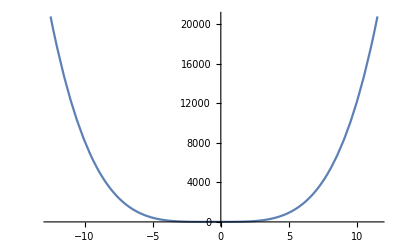

```mathematica
Plot[x+2 x^2+2 x^3+x^4,{x,-12.5,11.5}]
```

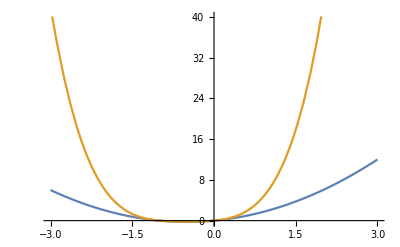

```mathematica
Plot[{x^2+x,x+2 x^2+2 x^3+x^4},{x,-3,3}]
```

```mathematica
Sum[x^i,{x,0,n}]
```

0^i+HarmonicNumber[n,-i]

```mathematica
DiscretePlot3D[0^i+HarmonicNumber[n,-i],{i,1,20},{n,1,20}]
```

-Graphics3D-

```mathematica
x^2+1/.x->(x^2+1)
```

1+(1+x^2)^2

```mathematica
Expand[1+(1+x^2)^2]
```

2+2 x^2+x^4

```mathematica
D[(2+2 x^2+x^4), x]
```

4 x+4 x^3

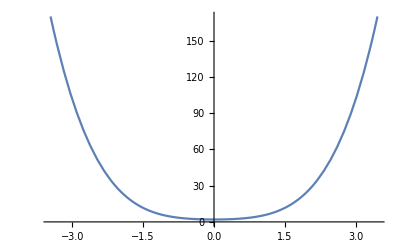

```mathematica
Plot[2+2 x^2+x^4,{x,-3.464101615137755,3.464101615137755}]
```

```mathematica
Roots[2+2 x^2+x^4==0,x]
```

x==√(-1-ⅈ)||x==-√(-1-ⅈ)||x==√(-1+ⅈ)||x==-√(-1+ⅈ)

```mathematica
Decompose[2+2 x^2+x^4,x]
```

{2+2 x+x^2,x^2}

```mathematica
x^(α n)
```

x^(n α)

```mathematica
FullSimplify[x^(α n),x∈Reals∧{α,n}∈]
```

x^(n α)

```mathematica
x+1
```

1+x

```mathematica
x+1/.x->(x+1)
```

2+x

```mathematica
x[x]+1
```

1+x[x]

```mathematica
a==1/(1-a)
```

a==1/(1-a)

```mathematica
Reduce[a==1/(1-a)]
```

a==(-1)^(1/3)||a==-(-1)^(2/3)

```mathematica
a[n]==1/(1-a[n-1])
```

a[n]==1/(1-a[-1+n])

```mathematica
Reduce[a[n]==1/(1-a[-1+n])]
```

a[n]≠0&&a[-1+n]==(-1+a[n])/a[n]

```mathematica
g[x]+1
```

1+g[x]

```mathematica
g[x]g[x]+g[x]
```

g[x]+g[x]^2

```mathematica
g[x]+g[x]^2/.g[x]->(g[x]+g[x]^2)
```

g[x]+g[x]^2+(g[x]+g[x]^2)^2

```mathematica
Expand[g[x]+g[x]^2+(g[x]+g[x]^2)^2]
```

g[x]+2 g[x]^2+2 g[x]^3+g[x]^4

```mathematica
Sum[x^i,{i,0,n}]
```

(-1+x^(1+n))/(-1+x)

```mathematica
Sum[x^i,{x,0,n}]
```

0^i+HarmonicNumber[n,-i]

```mathematica
(-1+x^(1+n))/(-1+x)/.x->((-1+x^(1+n))/(-1+x))
```

(-1+((-1+x^(1+n))/(-1+x))^(1+n))/(-1+(-1+x^(1+n))/(-1+x))

```mathematica
Asymptotic[x^i,{i,0,n},SeriesTermGoal->∞]
```

Asymptotic::aord: Approximation order specification n should be a positive integer.

Asymptotic[x^i,{i,0,n},SeriesTermGoal→∞]

```mathematica
DiscreteAsymptotic[x^i,{i,0,n},SeriesTermGoal->∞]
```

DiscreteAsymptotic::aord: Approximation order specification n should be a positive integer.

DiscreteAsymptotic[x^i,{i,0,n},SeriesTermGoal→∞]

```mathematica
FullSimplify[(-1+((-1+x^(1+n))/(-1+x))^(1+n))/(-1+(-1+x^(1+n))/(-1+x)),x∈Reals∧n∈]
```

((-1+x) (-1+((-1+x^(1+n))/(-1+x))^(1+n)))/(x (-1+x^n))

```mathematica
Nest[1/(1-#)&,x,10]
```

1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-1/(1-x))))))))))

```mathematica
Simplify/@NestList[1/(1-#)&,x,10]
```

{x,1/(1-x),(-1+x)/x,x,1/(1-x),(-1+x)/x,x,1/(1-x),(-1+x)/x,x,1/(1-x)}

```mathematica
1/x+x^2/.x->1/x+x^2
```

1/(1/x+x^2)+(1/x+x^2)^2

```mathematica
Simplify[1/(1/x+x^2)+(1/x+x^2)^2]
```

1/x^2+x^4+x (2+1/(1+x^3))

```mathematica
Expand[1/x^2+x^4+x (2+1/(1+x^3))]
```

1/x^2+2 x+x^4+x/(1+x^3)

```mathematica
recurse[h[x]+g[x]]==recurse[h[x]]+recurse[g[x]]+h[g[x]]+g[h[x]]
```

recurse[g[x]+h[x]]==g[h[x]]+h[g[x]]+recurse[g[x]]+recurse[h[x]]

```mathematica
D[x^(α n),x]
```

n x^(-1+n α) α

```mathematica
n x^(-1+n α) α==n x^(n α)/x α
```

True

```mathematica
recurse[h[x]+g[x]]==recurse[h[x]]+recurse[g[x]]+h[g[x]]+g[h[x]]
```

recurse[g[x]+h[x]]==g[h[x]]+h[g[x]]+recurse[g[x]]+recurse[h[x]]

```mathematica
recurse[h[x]+g[x]]==recurse[h[x]]+recurse[g[x]]+h[h[x]+g[x]]+g[h[x]+g[x]]
```

recurse[g[x]+h[x]]==g[g[x]+h[x]]+h[g[x]+h[x]]+recurse[g[x]]+recurse[h[x]]